# Encontrar raíces de las siguientes funciones:

## 1. x^2-2 2. x^10-1 3. e^x-x^2-x-1 4. x^3-x-1 5. cos(x)-x

```mathematica
Secante[x0_,x1_,cifras_]:=
Module[{},a=N[x0];b=N[x1];e=10^(-N[cifras]);n=1;
error=(b-a)/b;vector={{n,a,b,f[b],error}};
While[Abs[f[b]]>e&&Abs[error]>5*e&&n≤40,
c=(b*f[a]-a*f[b])/(f[a]-f[b]);a=b;
b=c;
error=(b-a)/b;
n=n+1;
vector=Append[vector,{n,a,b,f[b],error}];

];
Print[NumberForm[TableForm[vector,TableHeadings->{None, {"n","x(n-1)","xn","f(xn)","er"}}],16]];
];
```

```mathematica
f[x_]=0.6546 x(1-E^(-150/x))-36;
```

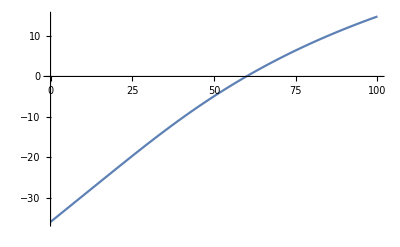

```mathematica
Plot[f[x],{x,0,100}]
```

```mathematica
Secante[59,61,4]
```

n | x(n-1) | xn | f(xn) | er
1 | 59. | 61. | 0.5157739529617658 | 0.03278688524590164
2 | 61. | 59.89447673662406 | 0.002768120259602824 | -0.01845784993226165
3 | 59.89447673662406 | 59.88851146069981 | -0.00001851460199020494 | -0.0000996063481750456

```mathematica
f[x_]= Sin[x] + Cos[1+x^2]-1;
```

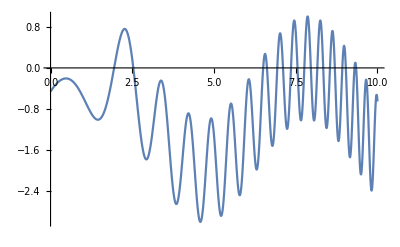

```mathematica
Plot[f[x],{x,0,10}]
```

```mathematica
Secante[1.5,2.5,3]
```

n | x(n-1) | xn | f(xn) | er
1 | 1.5 | 2.5 | 0.1663963173926513 | 0.4
2 | 2.5 | 2.356928734995134 | 0.6698423142602056 | -0.06070241449415816
3 | 2.356928734995134 | 2.547287160429604 | -0.0828279073758741 | 0.07472986492907454
4 | 2.547287160429604 | 2.526339088383083 | 0.03147109261088632 | -0.00829186871344644
5 | 2.526339088383083 | 2.532106931631685 | 0.0005700663577787868 | 0.002277882966374134

```mathematica
Secante[1.5,2.25,3]
```

n | x(n-1) | xn | f(xn) | er
1 | 1.5 | 2.25 | 0.7538208627396133 | 0.3333333333333333
2 | 2.25 | 1.92701799320814 | -0.06176948466194398 | -0.1676071567210187
3 | 1.92701799320814 | 1.951479332381875 | 0.02414683437924081 | 0.01253476722393913
4 | 1.951479332381875 | 1.944604457942254 | -0.000013943668801919 | -0.003535358777741628

```mathematica
f[x_]=x^10-1;
```

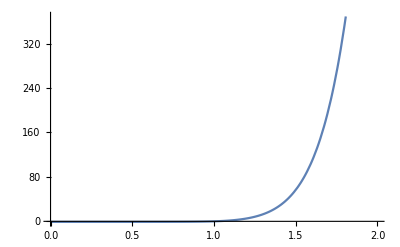

```mathematica
Plot[f[x],{x,0,2}]
```

```mathematica
Secante[0.8,1.2,5]
```

n | x(n-1) | xn | f(xn) | er
1 | 0.8 | 1.2 | 5.191736422399999 | 0.3333333333333333
2 | 1.2 | 0.858683279028436 | -0.7820634555751966 | -0.3974884911672549
3 | 0.858683279028436 | 0.90336695436091 | -0.6380554863787466 | 0.04946348227236802
4 | 0.90336695436091 | 1.10134672142893 | 1.625672967553799 | 0.1797615257901282
5 | 1.10134672142893 | 0.959169617595668 | -0.340895711957898 | -0.1482293655106118
6 | 0.959169617595668 | 0.983815370139325 | -0.1505534974483537 | 0.02505119689293616
7 | 0.983815370139325 | 1.003309228883456 | 0.03358945765228394 | 0.01942956187677593
8 | 1.003309228883456 | 0.999753360333352 | -0.002463661065475797 | -0.003556745784698947
9 | 0.999753360333352 | 0.999996347770012 | -0.00003652169963597185 | 0.0002429883241097573
10 | 0.999996347770012 | 1.000000004055392 | 4.055391844559608×10^-8 | 3.656285364522141×10^-6

n | x(n-1) | xn | f(xn) | er
1 | 1.1 | 1.2 | 5.191736422399999 | 0.0833333333333332
2 | 1.2 | 1.055704693315238 | 0.7195884637568033 | -0.1366815053475136
3 | 1.055704693315238 | 1.032486937770293 | 0.3767201219173604 | -0.02248721479720142
4 | 1.032486937770293 | 1.006976866899897 | 0.07200037427441952 | -0.02533332364320504
5 | 1.006976866899897 | 1.000949247539344 | 0.00953312639495163 | -0.006021903083868541
6 | 1.000949247539344 | 1.000029372578057 | 0.0002937646072898037 | -0.000919847942981143
7 | 1.000029372578057 | 1.000000125243342 | 1.252434127962943×10^-6 | -0.00002924733105217653

```mathematica
Solve[f[x]==0,x]
```

{{x→1/3 (27/2-(3 √69)/2)^(1/3)+(1/2 (9+√69))^(1/3)/3^(2/3)},{x→-1/6 (1+ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1-ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))},{x→-1/6 (1-ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1+ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))}}

```mathematica
SecanteModificad[x0_,cifras_]:=
Module[{},a=N[x0];e=10^(-N[cifras]);n=1;b=a;delta=0.001;
error=-1;vector={{n,a,b,f[b],error}};
While[Abs[f[b]]>e&&Abs[error]>5*e&&n≤40,
b=a-(delta*a*f[a])/(f[a+delta*a]-f[a]);
error=(b-a)/b;
a=b;
n=n+1;
vector=Append[vector,{n,a,b,f[b],error}];

];
Print[NumberForm[TableForm[vector,TableHeadings->{None, {"n","x(n-1)","xn","f(xn)","er"}}],16]];
];
```

```mathematica
f[x_]:=x^3-x-1;
```

```mathematica
SecanteModificad[1,5]
```

n | x(n-1) | xn | f(xn) | er
1 | 1. | 1. | -1. | -1
2 | 1.499250874063564 | 1.499250874063564 | 0.870695050798598 | 0.3330002221111907
3 | 1.347825781024509 | 1.347825781024509 | 0.1006808117229876 | -0.1123476751750163
4 | 1.325228071553986 | 1.325228071553986 | 0.002176484589897942 | -0.01705193993062982
5 | 1.324718828319014 | 1.324718828319014 | 3.714815082878076×10^-6 | -0.0003844160919934056

```mathematica
Secante[1,1.2,5]
```

n | x(n-1) | xn | f(xn) | er
1 | 1. | 1.2 | -0.472 | 0.1666666666666666
2 | 1.2 | 1.378787878787879 | 0.2423651111667635 | 0.1296703296703296
3 | 1.378787878787879 | 1.31812989949922 | -0.02792344616465914 | -0.04601821058129706
4 | 1.31812989949922 | 1.324396460821115 | -0.00137065352207788 | 0.00473163550890936
5 | 1.324396460821115 | 1.324719940330889 | 8.45715023500837×10^-6 | 0.000244187091872285

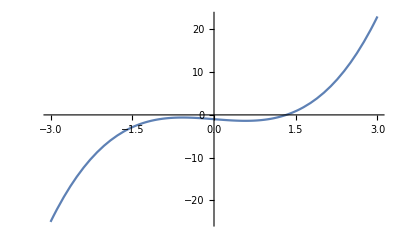

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
Secante[-1,-0.8,5]
```

n | x(n-1) | xn | f(xn) | er
1 | -1. | -0.8 | -0.7120000000000001 | -0.25
2 | -0.8 | -0.3055555555555555 | -0.7229723936899863 | -1.618181818181819
3 | -0.3055555555555555 | -32.88456189151607 | -35529.29686910038 | 0.990708236996936
4 | -32.88456189151607 | -0.3048926040319951 | -0.7234500599905083 | -106.8562138164073
5 | -0.3048926040319951 | -0.3042292009895338 | -0.7239288564486345 | -0.00218060278337365
6 | -0.3042292009895338 | -1.307278822060431 | -1.926831818304339 | 0.7672805557195277
7 | -1.307278822060431 | 0.2994242840953214 | -1.272579429276482 | 5.365974610276633
8 | 0.2994242840953214 | 3.424605569083156 | 35.73890589087459 | 0.912566782347585
9 | 3.424605569083156 | 0.4068785346241442 | -1.339519735465636 | -7.416776206310933
10 | 0.4068785346241442 | 0.5158989380156629 | -1.378591551285264 | 0.2113212401848534
11 | 0.5158989380156629 | -3.33072563984075 | -34.61945626369788 | 1.154890853766127
12 | -3.33072563984075 | 0.6754292086592816 | -1.367295285948409 | 5.93127273315911
13 | 0.6754292086592816 | 0.840158251165685 | -1.247119201984753 | 0.1960690647004281
14 | 0.840158251165685 | 2.549622774043857 | 13.02439457915358 | 0.67047742916371
15 | 2.549622774043857 | 0.989540164275047 | -1.020592591351143 | -1.576573307574384
16 | 0.989540164275047 | 1.102905077613632 | -0.7613317710882097 | 0.1027875522922369
17 | 1.102905077613632 | 1.435806555607087 | 0.5241667588676471 | 0.2318567753388603
18 | 1.435806555607087 | 1.300064752193223 | -0.102736442221208 | -0.1044115711812551
19 | 1.300064752193223 | 1.322310020552372 | -0.01024593746228097 | 0.0168230354556764
20 | 1.322310020552372 | 1.324774312741431 | 0.0002403481326829215 | 0.001860160002618881
21 | 1.324774312741431 | 1.324717830584745 | -5.401583558217737×10^-7 | -0.00004263712270000202

```mathematica
f[x_]=0.6546 x(1-E^(-150/x))-36;
```

```mathematica
Plot[f[x],{x,-0,100}]
```

```mathematica
Secante[59.5,61.5,4]
```

Secante[59.5,61.5,4]

```mathematica
f[x_]= Sin[x] + Cos[1+x^2]-1;
```

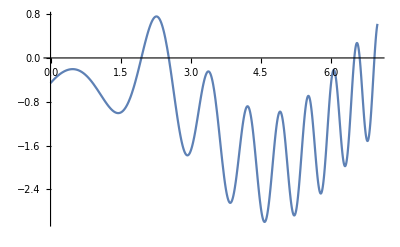

```mathematica
Plot[f[x],{x,0,7}]
```

```mathematica
Secante[1,3,3]
```

n | x(n-1) | xn | f(xn) | er
1 | 1. | 3. | -1.697951521016585 | 0.6666666666666666
2 | 3. | -0.02321427848421942 | -0.4833634370740872 | 130.2308094795768
3 | -0.02321427848421942 | -1.226347475638796 | -2.744750011957847 | 0.981070390778007
4 | -1.226347475638796 | 0.2339512163027409 | -0.2747172728181111 | 6.241893994053274
5 | 0.2339512163027409 | 0.3963657737266855 | -0.2119403256164519 | 0.409759288489772
6 | 0.3963657737266855 | 0.944691165764433 | -0.505811697070151 | 0.5804281990866816
7 | 0.944691165764433 | 0.000912955177605714 | -0.4587854404365233 | -1033.761825045945
8 | 0.000912955177605714 | -9.20653269357612 | -1.808529396762301 | 1.00009916384463
9 | -9.20653269357612 | 3.130574686546197 | -1.182823761466173 | 3.940844290711751
10 | 3.130574686546197 | 26.45244192538306 | -1.019134632838822 | 0.881652714884437
11 | 26.45244192538306 | 171.655259026801 | -0.1349250559429416 | 0.845897864852175
12 | 171.655259026801 | 193.81233437681 | -2.803392088963165 | 0.1143223181396243
13 | 193.81233437681 | 170.5349361619732 | -0.3527772198520847 | -0.1364963610314313
14 | 170.5349361619732 | 167.1840482149827 | -2.356001998896117 | -0.02004310807620561
15 | 167.1840482149827 | 171.1250431466418 | 0.4076325701320759 | 0.02302991344336408
16 | 171.1250431466418 | 170.5437514263567 | 0.04328685712348978 | -0.003408460969243285